# Introduction to Computational Physical Chemistry

© 2017 by Joshua Schrier and University Science Books  (Version: 25 July 2017)
Publisher’s Website: http://www.uscibooks.com/schrier.htm

## Chapter 6 - Hückel Molecular Orbital Theory

## 6.2 ELEMENTARY EXAMPLES

### 6.2.1 Ethylene

```mathematica
MatrixForm[hMatr={{0,1},{1,0}}] (*ethylene Hamiltonian*)
```

(0 | 1
1 | 0)

```mathematica
t=-2.7;(*typical π-π Hamiltonian matrix element,in eV*)
{evals,evecs}=Eigensystem[t*hMatr] (*get eigenvalues/vectors*)
```

{{-2.7,2.7},{{-0.707107,-0.707107},{-0.707107,0.707107}}}

```mathematica
evecs[[1]].evecs[[1]] (*check normalization for first MO...*)
evecs[[2]].evecs[[2]] (*...and second MO*)
```

1.

1.

```mathematica
evals[[2]]-evals[[1]] (*in eV,since t is defined in eV units*)
```

5.4

### 6.2.2 Butadiene

```mathematica
t=-2.7;
MatrixForm[hMatr={{0,1,0,0},{1,0,1,0},{0,1,0,1},{0,0,1,0}}]
{evals,evecs}=Eigensystem[t*hMatr]
```

(0 | 1 | 0 | 0
1 | 0 | 1 | 0
0 | 1 | 0 | 1
0 | 0 | 1 | 0)

{{4.36869,-4.36869,1.66869,-1.66869},{{-0.371748,0.601501,-0.601501,0.371748},{0.371748,0.601501,0.601501,0.371748},{0.601501,-0.371748,-0.371748,0.601501},{0.601501,0.371748,-0.371748,-0.601501}}}

```mathematica
sortEigen=Ordering[evals];(*find ascending sorting pattern*)
evals=evals[[sortEigen]] (*sort eigenvalues*)
evecs=evecs[[sortEigen]] (*sort eigenvectors*)
```

{-4.36869,-1.66869,1.66869,4.36869}

{{0.371748,0.601501,0.601501,0.371748},{0.601501,0.371748,-0.371748,-0.601501},{0.601501,-0.371748,-0.371748,0.601501},{-0.371748,0.601501,-0.601501,0.371748}}

```mathematica
sortedEigensystem[hamiltonian_]:=Module[{evals,evecs,sortEigen},
{evals,evecs}=Eigensystem[hamiltonian];
sortEigen=Ordering[evals];(*find ascending sorting pattern*)
evals=evals[[sortEigen]];(*sort eigenvalues*)
evecs=evecs[[sortEigen]];(*sort eigenvectors*)
{evals,evecs} (*return list of sorted eigenvalues and eigenvectors*)]
```

```mathematica
{evals,evecs}=sortedEigensystem[t*hMatr]
```

{{-4.36869,-1.66869,1.66869,4.36869},{{0.371748,0.601501,0.601501,0.371748},{0.601501,0.371748,-0.371748,-0.601501},{0.601501,-0.371748,-0.371748,0.601501},{-0.371748,0.601501,-0.601501,0.371748}}}

```mathematica
evals[[3]]-evals[[2]] (*HOMO-LUMO gap,in eV*)
```

3.33738

### 6.2.3 Benzene

```mathematica
t=-2.7; hMatr=({{0, 1, 0, 0, 0, 1}, {1, 0, 1, 0, 0, 0}, {0, 1, 0, 1, 0, 0}, {0, 0, 1, 0, 1, 0}, {0, 0, 0, 1, 0, 1}, {1, 0, 0, 0, 1, 0}});
{evals, evecs} = sortedEigensystem[t*hMatr]
```

{{-5.4,-2.7,-2.7,2.7,2.7,5.4},{{-0.408248,-0.408248,-0.408248,-0.408248,-0.408248,-0.408248},{0.288675,-0.288675,-0.57735,-0.288675,0.288675,0.57735},{0.5,0.5,-1.64477×10^-16,-0.5,-0.5,0.},{-0.5,0.5,1.64477×10^-16,-0.5,0.5,0.},{0.288675,0.288675,-0.57735,0.288675,0.288675,-0.57735},{0.408248,-0.408248,0.408248,-0.408248,0.408248,-0.408248}}}

```mathematica
evecs[[1]].evecs[[1]] (*check normalization*) 
evecs[[2]].evecs[[2]]
evecs[[3]].evecs[[3]]
```

1.

1.

1.

```mathematica
evecs[[1]].evecs[[2]] (*check orthogonality*) 
evecs[[2]].evecs[[3]]
```

3.88578×10^-16

-2.77556×10^-17

## 6.3 ADVANCED MATHEMATICA TECHNIQUES

### 6.3.1 Using ChemicalData[]

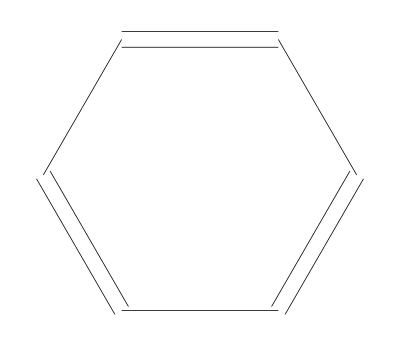

```mathematica
struct2d=ChemicalData["Benzene","StructureDiagram"]
```

```mathematica
struct3d=ChemicalData["Benzene","MoleculePlot"]
```

-Graphics3D-

```mathematica
MatrixForm[ChemicalData["Benzene","AdjacencyMatrix"]]
```

(0 | 2 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
2 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 2 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
types=ChemicalData["Benzene","VertexTypes"]
```

{C,C,C,C,C,C,H,H,H,H,H,H}

```mathematica
MatrixForm[
hMatr=Normal[
Take[ChemicalData["Benzene","AdjacencyMatrix"],{1,6},{1,6}]]]
```

(0 | 2 | 1 | 0 | 0 | 0
2 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 2 | 0
0 | 1 | 0 | 0 | 0 | 2
0 | 0 | 2 | 0 | 0 | 1
0 | 0 | 0 | 2 | 1 | 0)

```mathematica
MatrixForm[ hMatrBenzene=Unitize[hMatr] ]
```

(0 | 1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1 | 0)

```mathematica
t=-2.7;
{evalsBenzene,evecsBenzene}=sortedEigensystem[t*hMatrBenzene]
```

{{-5.4,-2.7,-2.7,2.7,2.7,5.4},{{0.408248,0.408248,0.408248,0.408248,0.408248,0.408248},{0.,-0.5,0.5,-0.5,0.5,0.},{-0.57735,-0.288675,-0.288675,0.288675,0.288675,0.57735},{5.81516×10^-17,0.5,-0.5,-0.5,0.5,0.},{0.57735,-0.288675,-0.288675,-0.288675,-0.288675,0.57735},{0.408248,-0.408248,-0.408248,0.408248,0.408248,-0.408248}}}

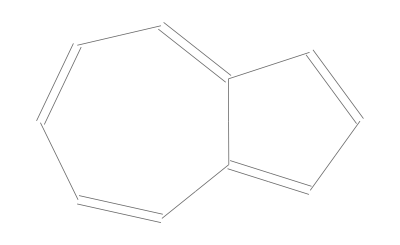

C_10H_8

```mathematica
ChemicalData["Azulene"]
ChemicalData["Azulene","CompoundFormulaDisplay"]
```

```mathematica
t=-2.7;
hMatrAzulene=Unitize[Normal[Take[ChemicalData["Azulene","AdjacencyMatrix"],{1,10},{1,10}]]];
{evalsAzulene,evecsAzulene}=sortedEigensystem[t*hMatrAzulene];
```

### 6.3.2 2D graphics in Mathematica

```mathematica
Graphics[{Blue,Disk[{1,1},1]}]
```

-Graphics-

```mathematica
blueCenter={1.25,1.25};redCenter={0,0};
Graphics[{Blue,Opacity[0.7],Disk[blueCenter,1],Red,Opacity[0.2],Disk[redCenter,2]}]
```

-Graphics-

```mathematica
xy=ChemicalData["Benzene","VertexCoordinates"] (*atom coords*)
```

{{100.,286.6},{50.,200.},{50.,373.21},{-50.,200.},{-50.,373.21},{-100.,286.6},{162.,286.6},{81.,146.31},{81.,426.9},{-81.,146.31},{-81.,426.9},{-162.,286.6}}

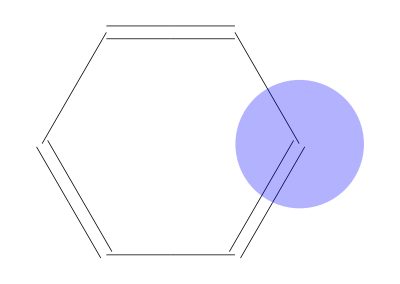

```mathematica
Show[ struct2d,Graphics[{Blue,Opacity[0.3],Disk[xy[[1]],50]}] ]
```

### 6.3.3 Application: Plotting molecular orbitals

```mathematica
scaledRadius[referenceArea_,desiredArea_,arbitraryRadius_:50]:=Sqrt[desiredArea/referenceArea]*arbitraryRadius;
```

```mathematica
plotMO[whichMO_,xyCoords_,coeffs_,nBasis_]:=Module[{graphicsList={},refArea=1/Sqrt[nBasis]},
Do[(*loop over the atoms*)
If[coeffs[[whichMO]][[r]]>0,(*check if positive sign*)AppendTo[graphicsList,Blue],(*if true, i.e., >0*)
AppendTo[graphicsList,Red] (*if false, i.e., <0*)];
AppendTo[graphicsList,Opacity[0.3]];AppendTo[graphicsList,Disk[xyCoords[[r]],
N[scaledRadius[refArea,Abs[coeffs[[whichMO]][[r]]]]]]];,{r,1,nBasis}];
Graphics[graphicsList] (*return composite graphical object*)
];
```

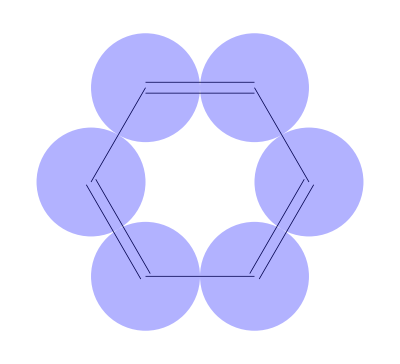

```mathematica
t=-2.7;
struct2d=ChemicalData["Benzene","StructureDiagram"];
xy=ChemicalData["Benzene","VertexCoordinates"];
Show[struct2d,plotMO[1,xy,evecsBenzene,6]]
```

```mathematica
GraphicsGrid[
Transpose[Prepend[
Table[{evalsBenzene[[i]],
Show[struct2d,plotMO[i,xy,evecsBenzene,6]]},{i,1,6}],{"Energy/eV","MO Diagram"}]]]
```

-Graphics-

## 6.4 HETEROATOMIC AROMATIC MOLECULES IN HUCKEL THEORY

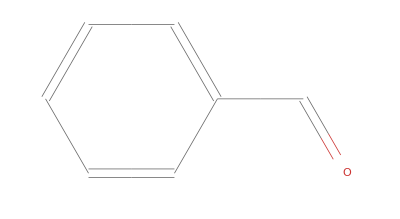

{O,C,C,C,C,C,C,C,H,H,H,H,H,H}

```mathematica
ChemicalData["Benzaldehyde"]
ChemicalData["Benzaldehyde","VertexTypes"]
```

```mathematica
t=-2.7;
MatrixForm[hMatrBenzaldehyde=Unitize[Take[Normal[
ChemicalData["Benzaldehyde","AdjacencyMatrix"]],{1,8},{1,8}]]];hMatrBenzaldehyde[[1,1;;8]]*=1;(*C=O bond off-diagonal matrix element*)
hMatrBenzaldehyde[[1;;8,1]]*=1;
hMatrBenzaldehyde[[1,1]]=1;(*oxygen atom on-diagonal matrix element*)
MatrixForm[hMatrBenzaldehyde]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
{evalsBenzaldehyde,evecsBenzaldehyde}=sortedEigensystem[t*hMatrBenzaldehyde];
```

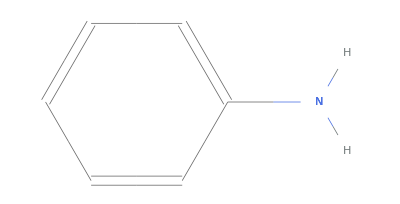

{N,C,C,C,C,C,C,H,H,H,H,H,H,H}

```mathematica
ChemicalData["Aminobenzene"] (*i.e., aniline*)
ChemicalData["Aminobenzene","VertexTypes"]
```

```mathematica
t=-2.7;
hMatrAniline=Unitize[Take[Normal[
ChemicalData["Aminobenzene","AdjacencyMatrix"]],{1,7},{1,7}]];hMatrAniline[[1,1;;7]]*=0.8; (*C-N (amine) matrix elements*)
hMatrAniline[[1;;7,1]]*=0.8;
hMatrAniline[[1,1]]=1.5; (*N (amine) atom matrix element*)
MatrixForm[hMatrAniline]
```

(1.5 | 0.8 | 0. | 0. | 0. | 0. | 0.
0.8 | 0 | 1 | 1 | 0 | 0 | 0
0. | 1 | 0 | 0 | 1 | 0 | 0
0. | 1 | 0 | 0 | 0 | 1 | 0
0. | 0 | 1 | 0 | 0 | 0 | 1
0. | 0 | 0 | 1 | 0 | 0 | 1
0. | 0 | 0 | 0 | 1 | 1 | 0)

```mathematica
{evalsAniline,evecsAniline}=sortedEigensystem[t*hMatrAniline];
```

## 6.5 INTERPRETING THE CHARGE DENSITY MATRIX

### 6.5.1 Construction

```mathematica
chargeDensMatr[coeffs_,nOcc_,nBasis_]:=Table[
Sum[2*coeffs[[i,r]]*coeffs[[i,s]],{i,1,nOcc}],
{r,1,nBasis},{s,1,nBasis}]//Chop;
```

```mathematica
MatrixForm[SetPrecision[
pMatrBenzene=chargeDensMatr[evecsBenzene,3,6] ,2]]
```

(1. | 0.67 | 0.67 | 0 | 0 | -0.33
0.67 | 1. | 0 | 0.67 | -0.33 | 0
0.67 | 0 | 1. | -0.33 | 0.67 | 0
0 | 0.67 | -0.33 | 1. | 0 | 0.67
0 | -0.33 | 0.67 | 0 | 1. | 0.67
-0.33 | 0 | 0 | 0.67 | 0.67 | 1.)

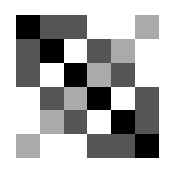

```mathematica
ArrayPlot[pMatrBenzene]
```

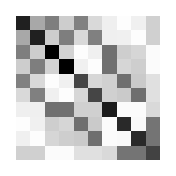

```mathematica
ArrayPlot[ pMatrAzulene=chargeDensMatr[evecsAzulene,5,10] ]
```

### 6.5.2 Electron density

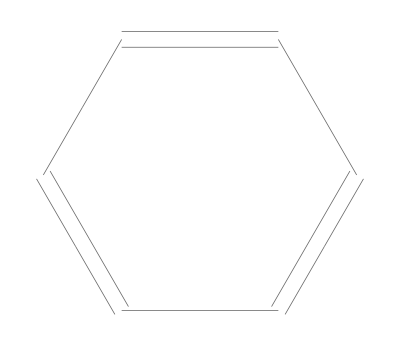

{1.,1.,1.,1.,1.,1.}

6.

```mathematica
ChemicalData["Benzene"]
Diagonal[pMatrBenzene]
Tr[pMatrBenzene]
```

```mathematica
ChemicalData["Azulene"]
Diagonal[pMatrAzulene]
Tr[pMatrAzulene]
```

-Graphics-

{1.02743,1.02743,1.17288,1.17288,0.854946,0.854946,1.0466,0.986447,0.986447,0.870001}

10.

```mathematica
plotCharge[netCharges_,xyCoords_,nAtoms_]:=Module[
{graphicsList={},refArea=1},
Do[(*loop over the atoms*)
If[netCharges[[r]]>0,
AppendTo[graphicsList,Black],(*excess electrons*)AppendTo[graphicsList,LightGray]]; (*deficient electrons*)

AppendTo[graphicsList,Opacity[1]];AppendTo[graphicsList,Disk[xyCoords[[r]],
N[scaledRadius[refArea,Abs[netCharges[[r]]]]]]];,
{r,1,nAtoms}];

Graphics[graphicsList]
];
```

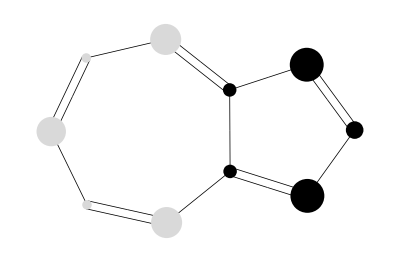

```mathematica
azuleneChargePlot=Show[
ChemicalData["Azulene","StructureDiagram"],
plotCharge[Diagonal[pMatrAzulene]-1,
ChemicalData["Azulene","VertexCoordinates"],10 ]
]
```

### 6.5.3 Dipole moment

```mathematica
calcDipoleVector2D[netCharges_,xyCoords_,nAtoms_]:=Sum[netCharges[[r]]*xyCoords[[r]],{r,1,nAtoms}];
```

```mathematica
azuleneDipole=calcDipoleVector2D[ Diagonal[pMatrAzulene]-1,ChemicalData["Azulene","VertexCoordinates"],10]
dipoleMoment=Sqrt[azuleneDipole.azuleneDipole] (*units of charge/pm*)
```

{95.7645,0.476481}

95.7657

```mathematica
plotDipoleVector2D[dipoleVec_,xyCoords_,nAtoms_]:=Graphics[ {Thick,Green,Arrowheads[.1],Arrow[{Mean[xyCoords]-dipoleVec/2,Mean[xyCoords]+dipoleVec/2}]} ];
```

```mathematica
Show[
ChemicalData["Azulene","StructureDiagram"],
plotDipoleVector2D[azuleneDipole,
ChemicalData["Azulene","VertexCoordinates"],10] ]
```

### 6.5.4 Bond order/length/strength

```mathematica
ChemicalData["Benzene"]
MatrixForm[
SetPrecision[nnBOMatrBenzene=pMatrBenzene*Unitize[hMatrBenzene],2] ]
```

-Graphics-

(0 | 0.67 | 0.67 | 0 | 0 | 0
0.67 | 0 | 0 | 0.67 | 0 | 0
0.67 | 0 | 0 | 0 | 0.67 | 0
0 | 0.67 | 0 | 0 | 0 | 0.67
0 | 0 | 0.67 | 0 | 0 | 0.67
0 | 0 | 0 | 0.67 | 0.67 | 0)

```mathematica
ChemicalData["Azulene"]
MatrixForm[
SetPrecision[nnBOMatrAzulene=pMatrAzulene*Unitize[hMatrAzulene],2] ]
```

-Graphics-

(0 | 0.4 | 0.6 | 0 | 0.59 | 0 | 0 | 0 | 0 | 0
0.4 | 0 | 0 | 0.6 | 0 | 0.59 | 0 | 0 | 0 | 0
0.6 | 0 | 0 | 0 | 0 | 0 | 0.66 | 0 | 0 | 0
0 | 0.6 | 0 | 0 | 0 | 0 | 0.66 | 0 | 0 | 0
0.59 | 0 | 0 | 0 | 0 | 0 | 0 | 0.66 | 0 | 0
0 | 0.59 | 0 | 0 | 0 | 0 | 0 | 0 | 0.66 | 0
0 | 0 | 0.66 | 0.66 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.66 | 0 | 0 | 0 | 0 | 0.64
0 | 0 | 0 | 0 | 0 | 0.66 | 0 | 0 | 0 | 0.64
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.64 | 0.64 | 0)

```mathematica
plotBondOrders[nnBondOrderMatr_,xyCoords_,nAtoms_]:=Module[
{graphicsList={}},
Do[
AppendTo[graphicsList,Orange];AppendTo[graphicsList,Opacity[0.5]];AppendTo[graphicsList,
Disk[Mean[{xyCoords[[r]],xyCoords[[s]]}],N[scaledRadius[1.6,Abs[nnBondOrderMatr[[r,s]]]]]]];
,{r,1,nAtoms-1},{s,r+1,nAtoms}];
Graphics[graphicsList]
];
```

```mathematica
Show[
ChemicalData["Azulene","StructureDiagram"],
plotBondOrders[nnBOMatrAzulene,
ChemicalData["Azulene","VertexCoordinates"],10] ]
```

-Graphics-

## 6.6 MOLECULAR REACTIVITY

### 6.6.1 Charge density and polar reactions

```mathematica
(*CONTENT IN THIS CELL DOES NOT APPEAR IN THE BOOK*)
hMatrNaphthalene=Unitize[Normal[Take[ChemicalData["Naphthalene","AdjacencyMatrix"],{1,10},{1,10}]]];
{evalsNaphthalene,evecsNaphthalene}=sortedEigensystem[-2.7*hMatrNaphthalene];
pMatrNaphthalene = chargeDensMatr[evecsNaphthalene,5,10];
(*aniline and benzaldehye evecs/evals computed in Section 6.4*)
pMatrAniline=chargeDensMatr[evecsAniline,4,7];
pMatrBenzaldehye = chargeDensMatr[evecsBenzaldehyde,4,8];
 
chargePlotGen[pMatr_,name_,chargeVec_]:=
Show[
ChemicalData[name,"StructureDiagram"],
plotCharge[Diagonal[pMatr]-chargeVec,
ChemicalData[name,"VertexCoordinates"],Length[pMatr] ]
]

naphthaleneChargePlot = chargePlotGen[pMatrNaphthalene,"Naphthalene",1];
anilineChargePlot = chargePlotGen[pMatrAniline,"Aminobenzene",{2,1,1,1,1,1,1}];
benzaldehydeChargePlot=chargePlotGen[pMatrBenzaldehye,"Benzaldehyde",1];
(*RESUME MATERIAL IN BOOK*)
```

```mathematica
(* Generate charge density matrices and use them to construct plots for napthalene,aniline, and benzaldehyde, storing the data in variables napthaleneChargePlot, etc. *)
GraphicsGrid[
{{"Naphthalene",naphthaleneChargePlot},
{"Azulene",azuleneChargePlot},
{"Aniline",anilineChargePlot},
{"Benzaldehyde",benzaldehydeChargePlot} }]
```

### 6.6.2 Frontier molecular orbitals and polar reactions

{-6.21749,-4.36869,-3.51749,-2.7,-1.66869,1.66869,2.7,3.51749,4.36869,6.21749}

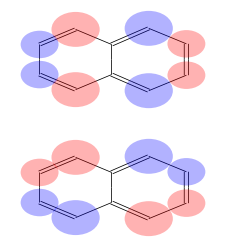

```mathematica
evalsNaphthalene
GraphicsGrid[
Prepend[
Table[
{evalsNaphthalene[[i]],Show[
ChemicalData["Naphthalene","StructureDiagram"],plotMO[i,ChemicalData["Naphthalene","VertexCoordinates"],evecsNaphthalene,10]]},
{i,6,5,-1}],
{"Energy/eV","MO Diagram"}]]
```

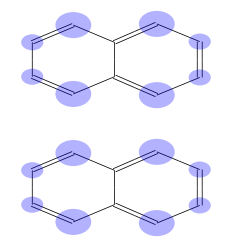

```mathematica
GraphicsGrid[
Prepend[
Table[
{evalsNaphthalene[[i]],Show[
ChemicalData["Naphthalene","StructureDiagram"],plotMO[i,ChemicalData["Naphthalene","VertexCoordinates"],evecsNaphthalene^2,10] ]},{
i,6,5,-1}],
{"Energy/eV","|ψ|^2 Diagram"}]]
```

### 6.6.3 Free valence index and radical attack

```mathematica
benzeneFreeValence=Table[
Sqrt[3]-Sum[nnBOMatrBenzene[[r,s]],{s,1,6}]
,{r,1,6}]
```

{0.398717,0.398717,0.398717,0.398717,0.398717,0.398717}

```mathematica
azuleneFreeValence=Table[
Sqrt[3]-Sum[nnBOMatrAzulene[[r,s]],{s,1,10}]
,{r,1,10}]
```

{0.149677,0.149677,0.48038,0.48038,0.482214,0.482214,0.419972,0.429112,0.429112,0.454253}

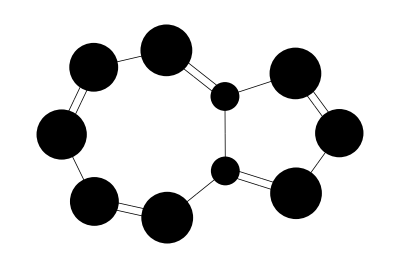

```mathematica
Show[
ChemicalData["Azulene","StructureDiagram"],
plotCharge[azuleneFreeValence,
ChemicalData["Azulene","VertexCoordinates"],10] ]
```